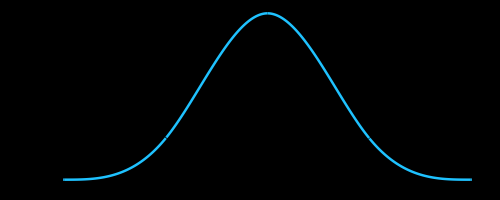

```mathematica
B3[x_]:=Piecewise[{{1/6(2-Abs[x])^3-4/6*(1-Abs[x])^3,-1≤x≤1},{1/6(2-Abs[x])^3,1<=Abs[x]≤2},{0, Abs[x]≥2}}]
Plot[B3[x],{x,-2.01,2.01},Background->Black,ImageSize->Full,PlotPoints->500,MaxRecursion->8,PlotStyle->Directive[RGBColor[0.12,0.76,1.],AbsoluteThickness[1.79]],AspectRatio->Automatic,Axes->True,AxesStyle->Directive[RGBColor[0.9745021744106203,0.9890592813000687,0.9950408178835737],AbsoluteThickness[0.]],Method->{"AxesInFront"->False},Frame->True,FrameStyle->White]
```